```mathematica
ClearAll["global`*"]
```

## Solution in external harmonic potential

```mathematica
M={{-(2*κ+k)/γ,0},{0,-k/γ}};
```

{{(-k-2 κ)/γ,0},{0,-k/γ}}

```mathematica
MatrixForm[M]
```

((-k-2 κ)/γ | 0
0 | -k/γ)

```mathematica
expM=MatrixExp[M*(t-tp)];
```

{{ⅇ^(-((t-tp) (k+2 κ))/γ),0},{0,ⅇ^(-(k t)/γ+(k tp)/γ)}}

```mathematica
covar=Integrate[expM.{{4/γ^2*2*(Subscript[T, 1]+Subscript[T, 2])/2*γ/2,1/γ^2*2*(Subscript[T, 1]-Subscript[T, 2])*γ/2},{1/γ^2*2*(Subscript[T, 1]-Subscript[T, 2])*γ/2,1/(4*γ^2)*2*(Subscript[T, 1]+Subscript[T, 2])/2*2*γ}}.Transpose[expM],{tp,-Infinity,t},Assumptions->{γ>0,k>0,κ>0}];
```

{{(T_1+T_2)/(k+2 κ),(T_1-T_2)/(2 (k+κ))},{(T_1-T_2)/(2 (k+κ)),(T_1+T_2)/(4 k)}}

```mathematica
P[R_,r_,kk_]:=Simplify[Exp[-1/2*{r,R}.Inverse[covar].{r,R}]]/.{k->kk}
```

## Patching and normalization

```mathematica
SubMinus[k]=2*Subscript[U, 0]/L^2;
```

(2 U_0)/L^2

```mathematica
SubPlus[k]=2*Subscript[U, 0]/l^2;
```

(2 U_0)/l^2

```mathematica
SubMinus[f]=Integrate[P[R,r,SubMinus[k]],{r,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}];
```

(ⅇ^(-(4 R^2 U_0)/(L^2 (T_1+T_2))) √((16 L^2 π T_1 T_2 U_0)/(T_1+T_2)+(L^6 π κ^2 (T_1+T_2))/(L^2 κ+U_0)))/(L^2 κ+2 U_0)

```mathematica
SubPlus[f]=Integrate[P[R,r,SubPlus[k]],{r,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}];
```

(ⅇ^(-(4 R^2 U_0)/(l^2 (T_1+T_2))) l √((16 π T_1 T_2 U_0)/(T_1+T_2)+(l^4 π κ^2 (T_1+T_2))/(l^2 κ+U_0)))/(l^2 κ+2 U_0)

```mathematica
{{SubMinus[exprA],SubPlus[exprA]}}=Simplify[Solve[SubMinus[A]*(SubMinus[f]/.{R->0})==SubPlus[A]*(SubPlus[f]/.{R->0})&&SubMinus[A]*Integrate[SubMinus[f],{R,-L,0},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}]+SubPlus[A]*Integrate[SubPlus[f],{R,0,l},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}]==1,{SubMinus[A],SubPlus[A]}],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}];
```

{{A_-→(4 (L^2 κ+2 U_0) √((U_0 (L^2 κ+U_0))/(L^4 κ^2 T_1^2+L^4 κ^2 T_2^2+2 T_1 T_2 (L^4 κ^2+8 L^2 κ U_0+8 U_0^2))))/(L (l+L) π Erf[2 √(U_0/(T_1+T_2))]),A_+→(4 U_0 √(l^2 κ+U_0) (l^2 κ+2 U_0))/(l (l+L) π Erf[2 √(U_0/(T_1+T_2))] √(U_0 (l^4 κ^2 T_1^2+l^4 κ^2 T_2^2+2 T_1 T_2 (l^4 κ^2+8 l^2 κ U_0+8 U_0^2))))}}

## Current

```mathematica
Subscript[J, R]=Simplify[-k*R/γ*P[R,r,k]-(Subscript[T, 1]+Subscript[T, 2])/(4*γ)*D[P[R,r,k],R]-(Subscript[T, 1]-Subscript[T, 2])/(2*γ)*D[P[R,r,k],r]];
```

(ⅇ^(-((k+κ) ((k^2 (r-2 R)^2+k (3 r^2-8 r R+4 R^2) κ+2 r^2 κ^2) T_1+(k^2 (r+2 R)^2+k (3 r^2+8 r R+4 R^2) κ+2 r^2 κ^2) T_2))/(2 (κ^2 T_1^2+2 (2 k^2+4 k κ+κ^2) T_1 T_2+κ^2 T_2^2))) κ (k+2 κ) (T_1-T_2) ((k (r-2 R)+r κ) T_1+(k (r+2 R)+r κ) T_2))/(2 γ (κ^2 T_1^2+2 (2 k^2+4 k κ+κ^2) T_1 T_2+κ^2 T_2^2))

```mathematica
{{SubPlus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R->l,k->SubPlus[k]})==0,r],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}];
```

{{r→(4 l (T_1-T_2) U_0)/((T_1+T_2) (l^2 κ+2 U_0))}}

```mathematica
{{SubMinus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R->-L,k->SubMinus[k]})==0,r],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}];
```

{{r→(4 L (-T_1+T_2) U_0)/((T_1+T_2) (L^2 κ+2 U_0))}}

```mathematica
Subscript[J, right]=Integrate[SubPlus[A]*Subscript[J, R]/.{R->l,k->SubPlus[k],SubPlus[exprA]},{r,r/.{SubPlus[exprr]},Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}];
```

(2 ⅇ^(-(4 U_0)/(T_1+T_2)) l κ (T_1-T_2) √((U_0 (l^2 κ+U_0))/(l^4 κ^2 (T_1+T_2)^2+16 l^2 κ T_1 T_2 U_0+16 T_1 T_2 U_0^2)))/((l+L) π γ Erf[2 √(U_0/(T_1+T_2))])

```mathematica
Subscript[J, left]=Integrate[SubMinus[A]*Subscript[J, R]/.{R->-L,k->SubMinus[k],SubMinus[exprA]},{r,-Infinity,r/.{SubMinus[exprr]}},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}];
```

(2 ⅇ^(-(4 U_0)/(T_1+T_2)) L κ (-T_1+T_2) √((U_0 (L^2 κ+U_0))/(L^4 κ^2 (T_1+T_2)^2+16 L^2 κ T_1 T_2 U_0+16 T_1 T_2 U_0^2)))/((l+L) π γ Erf[2 √(U_0/(T_1+T_2))])

```mathematica
Subscript[J, total]=Simplify[Subscript[J, right]+Subscript[J, left],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, 1]>Subscript[T, 2]>0}];
```

```mathematica
(2 ⅇ^(-(4 Subscript[U, 0])/(Subscript[T, 1]+Subscript[T, 2])) κ (Subscript[T, 1]-Subscript[T, 2]) (l √((Subscript[U, 0] (l^2 κ+Subscript[U, 0]))/(l^4 κ^2 (Subscript[T, 1]+Subscript[T, 2])^2+16 l^2 κ Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]+16 Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]^2))-L √((Subscript[U, 0] (L^2 κ+Subscript[U, 0]))/(L^4 κ^2 (Subscript[T, 1]+Subscript[T, 2])^2+16 L^2 κ Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]+16 Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]^2))))/((l+L) π γ Erf[2 √(Subscript[U, 0]/(Subscript[T, 1]+Subscript[T, 2]))]);
```

(2 ⅇ^(-(4 U_0)/(T_1+T_2)) κ (T_1-T_2) (l √((U_0 (l^2 κ+U_0))/(l^4 κ^2 (T_1+T_2)^2+16 l^2 κ T_1 T_2 U_0+16 T_1 T_2 U_0^2))-L √((U_0 (L^2 κ+U_0))/(L^4 κ^2 (T_1+T_2)^2+16 L^2 κ T_1 T_2 U_0+16 T_1 T_2 U_0^2))))/((l+L) π γ Erf[2 √(U_0/(T_1+T_2))])

```mathematica
Subscript[J, total]= (2 ⅇ^(-(4 Subscript[U, 0])/(Subscript[T, 1]+Subscript[T, 2])) κ (Subscript[T, 1]-Subscript[T, 2]) (l √((Subscript[U, 0] (l^2 κ+Subscript[U, 0]))/(l^4 κ^2 (Subscript[T, 1]+Subscript[T, 2])^2+16 l^2 κ Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]+16 Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]^2))-L √((Subscript[U, 0] (L^2 κ+Subscript[U, 0]))/(L^4 κ^2 (Subscript[T, 1]+Subscript[T, 2])^2+16 L^2 κ Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]+16 Subscript[T, 1] Subscript[T, 2] Subscript[U, 0]^2))))/((l+L) π γ Erf[2 √(Subscript[U, 0]/(Subscript[T, 1]+Subscript[T, 2]))]);
```

```mathematica
Subscript[J, paper]= Simplify[Subscript[J, total]/.{Subscript[T, 1]->T*(1-δ),Subscript[T, 2]->T*(1+δ),L->Subscript[λ, l],l->Subscript[λ, r]},{γ>0,κ>0,Subscript[U, 0]>0,Subscript[λ, l]>0,Subscript[λ, r]>0,T>0,δ>0}];
```

## Simplifying Notation

```mathematica
Subscript[J, paper]= Subscript[J, paper]/.{κ->κ*2*T/(Subscript[λ, l]+Subscript[λ, r])^2};
```

```mathematica
Subscript[J, total]= Subscript[J, total]/.{κ->κ*(Subscript[T, 1]+Subscript[T, 2])/(l+L)^2};
```

```mathematica
Subscript[J, total] = Subscript[J, total]/.{Subscript[T, 1]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, 2]->Subscript[T, 2]*Subscript[U, 0]};
```

```mathematica
Subscript[J, paper]= Subscript[J, paper]/.{T->Subscript[U, 0]*T};
```

```mathematica
Subscript[J, paper]= Simplify[Subscript[J, paper],{γ>0,Subscript[λ, r]>0,Subscript[λ, l]>0,δ>0,T>0,Subscript[u, 0]>0,κ>0}];
```

```mathematica
Subscript[J, better]= Simplify[Subscript[J, total]/.{Subscript[T, 1]->0.1,Subscript[T, 2]->T},{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,T>0}];
```

```mathematica
Subscript[J, sub]= Simplify[Subscript[J, better]/.{Subscript[U, 0]->1,γ->.01,l->1.0,L->9.0}];
```

```mathematica
Subscript[J, pot] = Simplify[Subscript[J, total]/.{Subscript[T, 1]->0.1,Subscript[T, 2]->1,Subscript[U, 0]->u,l->1,L->9,γ->0.01}]
```

-0.0016723 u^2 κ (-9. √((1.04102+0.927549 κ)/(u^2 (1.66563+1.48408 κ+1. κ^2)))+√((6830.13+75.1315 κ)/(u^2 (10928.2+120.21 κ+1. κ^2))))

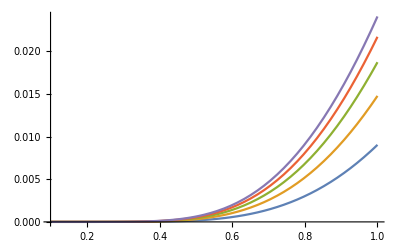

```mathematica
Plot[{Subscript[J, sub]/.{κ->1},Subscript[J, sub]/.{κ->2},Subscript[J, sub]/.{κ->3},Subscript[J, sub]/.{κ->4},Subscript[J, sub]/.{κ->5}},{T,0.1,1}]
```

## Importing Data

```mathematica
dt1 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_dt1","List"];
```

```mathematica
dt5 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_dt5","List"];
```

```mathematica
dt10 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_dt10","List"];
```

```mathematica
dt15 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_dt15","List"];
```

```mathematica
dt20 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_dt20","List"];
```

```mathematica
tvals = Array[#&,100,{0.1,1.1}];
```

```mathematica
pl1 = ListPlot[{Transpose@{tvals,dt15},Transpose@{tvals,dt20}}];
```

```mathematica
th1 = Plot[{Subscript[J, sub]/.{κ->15},Subscript[J, sub]/.{κ->20}},{T,0.1,1.1}];
```

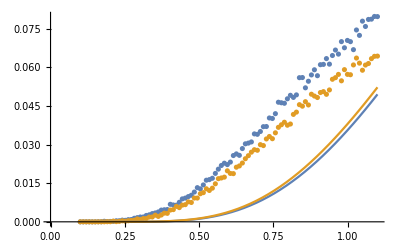

```mathematica
Show[pl1,th1]
```

```mathematica
du1 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_u1","List"];
```

```mathematica
du2 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_u2","List"];
```

```mathematica
du3 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_u3","List"];
```

```mathematica
du4 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_u4","List"];
```

```mathematica
du5 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_u5","List"];
```

```mathematica
uvals = Array[#&,100,{0,5}];
```

```mathematica
pl2 = ListPlot[{Transpose@{uvals,du1},Transpose@{uvals,du2}}];
```

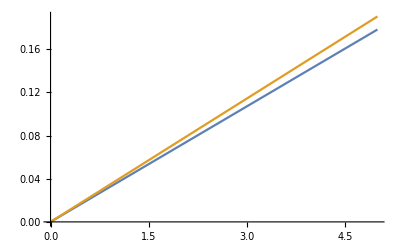

```mathematica
th2 = Plot[{Subscript[J, pot]/.{κ->15},Subscript[J, pot]/.{κ->20}},{u,0,5}]
```